# NeRF: Neural Radiance Fields

```mathematica
$HistoryLength=0;
```

## Caméra 1D dans un monde 2D

```mathematica
unCarré[]:={{-1,-1},{-1,1},{1,1},{1,-1},{-1,-1}};
unCercle[]:=CirclePoints[{1,1},32];
unTriangle[]:=CirclePoints[3];

unePetale[]:=Module[{r=0.5,d=1.0},Translate[CirclePoints[{r,r*2},32],{d,0}]];

(*Apply rotation transformations to the points*)
applyTransformations[points_,θ_]:=RotationTransform[θ][#]&/@points;

(*Generate all petals as a single flat list of points*)
petals=Flatten[Table[applyTransformations[unePetale[],θ],{θ,0,2Pi,Pi/4}],1];

removeTranslate[Translate[points_,translation_]]:=TranslationTransform[translation]/@points;

finalPoints=removeTranslate/@petals;
```

```mathematica
unTriangle[]
```

{{(√3)/2,-1/2},{0,1},{-(√3)/2,-1/2}}

```mathematica
Clear[place];
place[{posx_,posy_},angle_,{échellex_,échelley_}]:=TranslationTransform[{posx,posy}].RotationTransform[angle].ScalingTransform[{échellex,échelley}];
place[{posx_,posy_},angle_,échelle_]:=place[{posx,posy},angle,{échelle,échelle}];
place[{posx_,posy_},angle_]:=place[{posx,posy},angle,{1,1}];
place[{posx_,posy_}]:=place[{posx,posy},0,{1,1}];
```

```mathematica
see[e_]:={
If[KeyExistsQ[e,"couleur"],e[["couleur" ]],Black],If[KeyExistsQ[e,"densite"],Opacity[e[["densite"]]],Opacity[1]],
Polygon[e[["lignes" ]]]};

seeMonde[monde_,{{xmin_,xmax_},{ymin_,ymax_}}]:=Block[{},(
Graphics[{
GrayLevel[0.8],Rectangle[{xmin,ymin},{xmax,ymax}],
GrayLevel[0.9],Thick,
Line[{{0,ymin},{0,ymax}}],
Line[{{xmin,0},{xmax,0}}],
see/@monde
}]
)]
```

```mathematica
e2p[v_]:=Append[v,1];
p2e[v_]:=Delete[v,-1]/v[[-1]];
```

```mathematica
seeCam[w2i_TransformationFunction,width_,depth_]:=Block[{i2w,coinsCam,coinsW},(
i2w=InverseFunction[w2i];
coinsCam={{0,1}*depth,{0,0},{width,1}*depth};
coinsW=i2w[coinsCam];
Graphics[{
PointSize[0.025],
Blue,Point[coinsW[[2]]],
Opacity[0.4],Polygon[coinsW]
}]
)]
```

## Prise de Photo 1D

```mathematica
Clear[render]
render[rgba_,δ_,fond_]:=Block[{σ,α,t},(
σ=rgba[[All,4]];
α=1-Exp[-σ δ];
t=Prepend[Exp[-Accumulate[σ δ]],1];
Total[rgba[[All,{1,2,3}]]*t[[1;;-2]]α]+t[[-1]]*fond
)]
```

```mathematica
photo[w2i_TransformationFunction,segment_]:=Block[{p,q,m},(
m=TransformationMatrix[w2i]; (* 3x3 avec  (0,0,1)  derniere  rangee *) 
p=(m.e2p[#])&/@segment;  (* (xh,zh,h) *) 
q=p/p[[All,2]]; (* (x/z,1,1/z) *) 
{#[[1]],1/#[[3]]}&/@q   (* (x/z,z) *)
)]
```

```mathematica
imageDataAlpha[img_Image,Missing[___]]:=ImageData[img];
imageDataAlpha[img_Image,densite_]:=Map[(#*{1.,1.,1.,densite})&,ImageData[img],{2}];
```

```mathematica
mix[clouds_]:=Block[{t},(
t=Max[Total[clouds[[All,4]]],10.^-6];
Append[Total[clouds[[All,1;;3]]*clouds[[All,4]]]/t,t]
)];
```

```mathematica
snapshot[w2i_TransformationFunction,monde_,width_,δ_,fond_]:=Block[{vg,zrange,ratio,nzx,nzxc,zxnc,zxc},(
vg={#[["couleur" ]],Polygon[photo[w2i,#[["lignes" ]]]]}&/@monde;
zrange=MinMax[Table[(List@@vg[[i,2]])[[1,All,2]],{i,1,Length[vg]}]];
zrange[[1]]=Max[0.1,zrange[[1]]]; (* distance minimale de la cam *) 
ratio=((zrange[[2]]-zrange[[1]])/width)/δ;
nzx=Rasterize[Graphics[{#},AspectRatio->ratio,PlotRange->{{0,width},zrange}],RasterSize->{width,Automatic},Background->None]&/@vg;
nzxc=MapThread[(imageDataAlpha[#1,#2])&,{nzx,monde[[All,"densite"]]}];
zxnc=Flatten[nzxc,{{2},{3},{1},{4}}];
zxc=Map[mix,zxnc,{2}];
Image[{render[#,δ,fond]&/@Transpose[zxc]},ImageSize->Scaled[0.9]]
)]
```

## Data

```mathematica
zap[w2i_,is_]:=<|"Input"->TransformationMatrix[InverseFunction[w2i]],"Target"->ImageData[is,Interleaving->False][[All,1]]|>
seeOut[o_]:=Image[{Transpose[o]},ImageSize->Scaled[1]]
```

### Create World

```mathematica
monde={
<|"couleur" ->Red,
"densite" ->0.4,
"lignes"->place[{0,1},0]@unCarré[]|>,
<|"couleur" ->Red,
"densite" ->0.4,
"lignes"->place[{-1,0},0]@unTriangle[]|>,
<|"couleur" ->Red,
"densite" ->0.4,
"lignes"->place[{1,0},0]@unCercle[]|>
(*<|"couleur" ->Purple,
"densite" ->0.4,
"lignes"->place[{0,0},0]@finalPoints[[1]]|>,
(*<|"couleur" ->Purple,
"densite" ->0.2,
"lignes"->place[{0,0},0]@finalPoints[[2]]|>,*)
<|"couleur" ->Purple,
"densite" ->0.2,
"lignes"->place[{0,0},0]@finalPoints[[3]]|>,
(*<|"couleur" ->Purple,
"densite" ->0.4,
"lignes"->place[{0,0},0]@finalPoints[[4]]|>,*)
<|"couleur" ->Purple,
"densite" ->0.4,
"lignes"->place[{0,0},0]@finalPoints[[5]]|>,
(*<|"couleur" ->Purple,
"densite" ->0.9,
"lignes"->place[{0,0},0]@finalPoints[[6]]|>,*)
<|"couleur" ->Purple,
"densite" ->0.9,
"lignes"->place[{0,0},0]@finalPoints[[7]]|>*)
(*<|"couleur" ->Red,
"densite" ->0.9,
"lignes"->place[{1.5,1.5},0]@finalPoints[[8]]|>*)
};
```

### Create Cameras

```mathematica
s =1;
k = 0.1;
c2i=LinearFractionalTransform[({{50, 50, 0}, {0, 1, 0}, {0, 0, 1}})];
i2c=InverseFunction[c2i];
c2wS=Table[place[{Cos[t],Sin[t]}*4,t+Pi/2],{t,0,360 Degree,s Degree}]//N;
w2iS=InverseFunction[#.i2c]&/@c2wS;
```

### See

```mathematica
Show[
seeMonde[monde,{{-5,5},{-5,5}}],
seeCam[#,100,0.9]&/@w2iS[[1;;-1;;10]]
]
```

-Graphics-

### Generate Data

```mathematica
is=Parallelize[snapshot[#,monde,100,0.25,{0,0,0}]&/@w2iS];
data=MapThread[zap,{w2iS,is}];
data//Dimensions
data[[1,"Target"]]//Dimensions
```

{361}

{3,100}

### Train-Valid-Test Split

```mathematica
SeedRandom[1];
dataShuffled=RandomSample[data];

dataTrain=dataShuffled[[1;;-19]];
dataValid=dataShuffled[[-19;;-10]];
dataTest=dataShuffled[[-10;;-1]];

(* Question 7*)
(*grayscaleData=Table[ColorConvert[Transpose[dataShuffled[[i,"Target"]],{2,1}],"Grayscale"],{i,Length[dataShuffled]}];
grayscaleData=Table[Transpose[ImageData[Image[ColorConvert[Image[Transpose[dataShuffled[[i,"Target"]],{2,1}]],"Grayscale"],"Real"]],{2,1} ],{i,Length[dataShuffled]}];




dataShuffledGrayScale = dataShuffled;
dataShuffledGrayScale[[All,"Target", 1]] = grayscaleData[[All, 1, All]];
dataShuffledGrayScale[[All,"Target", 2]] =  grayscaleData[[All, 1, All]];
dataShuffledGrayScale[[All,"Target", 3]] =  grayscaleData[[All, 1, All]];


dataTrain=dataShuffledGrayScale[[1;;180]];
dataValid=dataShuffledGrayScale[[-19;;-10]];
dataTest=dataShuffledGrayScale[[-10;;-1]];*)



dataTrain//Dimensions
dataValid//Dimensions
dataTest //Dimensions
```

{180}

{10}

{10}

## NERF - Neural Network

```mathematica
(*equation 3 in https://arxiv.org/pdf/2003.08934*)
renderLayer[zStep_,n_,backgroundColor_]:=Block[{low,accumulate},(
low=LowerTriangularize[Table[1.,n,n]];
accumulate=NetGraph@FunctionLayer[Block[{rep,lower,times,acc},(
rep=ReplicateLayer[n]@#Input;
lower=NetArrayLayer["Array"->low,LearningRateMultipliers->0][];
times=ThreadingLayer[Times,None,InputPorts->{{n,n},{n,n}}][<|"Input1"->rep,"Input2"->lower|>];
acc=AggregationLayer[Total,2][times]
)]&];
NetGraph@FunctionLayer[Block[{density,alpha,transmitance,rgb,background,times,sum,out,value,transmitance2},(
density=#Input[[4]];
alpha=1-Exp[-density*zStep];
value=accumulate[density*zStep];
transmitance=Prepend[Exp[-value],1];
rgb=PartLayer[1;;3]@#Input;
background=transmitance[[-1]]*backgroundColor;
transmitance=PartLayer[1;;n][transmitance];
times=ThreadingLayer[Times,1,InputPorts->{{3,n},{n},{n}}][<|"Input1"->rgb,"Input2"->transmitance,"Input3"->alpha|>];
sum=AggregationLayer[Total,2][times];
out=ThreadingLayer[Plus,1,InputPorts->{{3},{3}}][<|"Input1"->sum,"Input2"->background|>];
out
)]&,"Input"->{4,n}]
)]
renderLayer[zStep_,n_]:=renderLayer[zStep,n,{0,0,0}]
```

```mathematica
camera2World[nbPixels_,zMin_,zMax_,zStep_]:=Block[{zRangeArray,xRangeArray},(
zRangeArray=NetArrayLayer["Array"->{Range[zMin,zMax,zStep]},LearningRateMultipliers->0];
xRangeArray=NetArrayLayer["Array"->{Range[0,100,100/(nbPixels-1)]},LearningRateMultipliers->0];
NetGraph@FunctionLayer[Block[{a1,a2,b1,b2,i2wm,z,x,stepz,newz,ones,xp,onesp,onespp,grid,out},(
i2wm=#Input[[1;;2]];
a2=i2wm[[1,2]];
a1=i2wm[[1,1]];
b2=i2wm[[2,2]];
b1=i2wm[[2,1]];
z=zRangeArray[];
x=xRangeArray[];
stepz=Sqrt[(a2+ a1*x)^2+(b2+b1* x)^2];
newz=Transpose[stepz].(z*0+1);
ones=x*0+1;
xp=Transpose[x].z;
onesp=Transpose[ones].z;
onespp=onesp*0+1;
grid={xp/newz,onesp/newz,onespp};
out=i2wm.grid;
<|"Output"->out|>
)]&,"Input"->{3,3}]
)]
```

```mathematica
positionalEncodingLayer[L_]:=Block[{idxLayer},(
idxLayer=NetArrayLayer["Array"->Table[N[Pi]*2^i,{i,0,L-1}],LearningRateMultipliers->0];
NetGraph@FunctionLayer[Block[{idx,x,y,xx,yy,xxx,yyy,xxxx,yyyy},(
x=FlattenLayer[{{2},{3},{1}}]@#Input[[1;;1]];
y=FlattenLayer[{{2},{3},{1}}]@#Input[[2;;2]];
idx=idxLayer[];
xx=ThreadingLayer[Times,1,InputPorts->{{Automatic,Automatic,1},{L}}][<|"Input1"->x,"Input2"->idx|>];
yy=ThreadingLayer[Times,1,InputPorts->{{Automatic,Automatic,1},{L}}][<|"Input1"->y,"Input2"->idx|>];
xxx={Sin[xx],Cos[xx]};
xxxx=FlattenLayer[{{1,4},{2},{3}}][xxx];
yyy={Sin[yy],Cos[yy]};
yyyy=FlattenLayer[{{1,4},{2},{3}}][yyy];
Join[xxxx,yyyy]
)]&,"Input"->{2,Automatic,Automatic}]
)]


(*Question 6*)
(*positionalEncodingLayer[L_]:=Block[{idxLayer},(idxLayer=NetArrayLayer["Array"->Table[N[Pi]*2^i,{i,0,L-1}],LearningRateMultipliers->0];
NetGraph@FunctionLayer[Block[{idx,x,y,xx,yy,xxx,yyy,xxxx,yyyy,finalOutput},(x=FlattenLayer[{{2},{3},{1}}]@#Input[[1;;1]];
y=FlattenLayer[{{2},{3},{1}}]@#Input[[2;;2]];
idx=idxLayer[];
xx=ThreadingLayer[Times,1,InputPorts->{{Automatic,Automatic,1},{L}}][<|"Input1"->x,"Input2"->idx|>];
yy=ThreadingLayer[Times,1,InputPorts->{{Automatic,Automatic,1},{L}}][<|"Input1"->y,"Input2"->idx|>];
xxx={Sin[xx],Cos[xx]};
xxxx=FlattenLayer[{{1,4},{2},{3}}][xxx];
yyy={Sin[yy],Cos[yy]};
yyyy=FlattenLayer[{{1,4},{2},{3}}][yyy];
finalOutput=ElementwiseLayer[Exp][Join[xxxx,yyyy]];
finalOutput)]&,"Input"->{2,Automatic,Automatic}])]*)
```

```mathematica
Clear[nerfSampler];
nerfSampler[nbPixels_,zMin_,zMax_,zStep_,L_]:=Block[{c2w,posE,end,mlp,render,relu},(
relu=Ramp;
c2w=camera2World[nbPixels,zMin,zMax,zStep];
posE=positionalEncodingLayer[L];
end=NetGraph@FunctionLayer[Join[LogisticSigmoid[#Input[[1;;3]]],Ramp[#Input[[4;;4]]]]&,"Input"->{4,Automatic,Automatic}];
mlp=NetChain[{
ConvolutionLayer[128,{1,1}],relu,
ConvolutionLayer[128,{1,1}],relu,
ConvolutionLayer[128,{1,1}],relu,
ConvolutionLayer[128,{1,1}],relu,
ConvolutionLayer[128,{1,1}],relu,
ConvolutionLayer[128,{1,1}],relu,
ConvolutionLayer[128,{1,1}],relu,
ConvolutionLayer[128,{1,1}],relu,
ConvolutionLayer[4,{1,1}],end
}];
render=NetMapOperator[renderLayer[zStep,Floor[1+((zMax-zMin)/zStep)],{0.,0.,0.}]];

NetGraph@FunctionLayer[Block[{p2D,p2Dencoded,rgba,rgbaF,out},(
p2D=c2w[#Input];
p2Dencoded=posE[p2D/5];
rgba=mlp[p2Dencoded];

rgbaF=FlattenLayer[{{2},{1},{3}}][rgba];
out=render[rgbaF];
<|"Output"->Transpose[out],"rgba"->rgba,"p2d"->p2D|>
)]&]
)]
(*Question 5*) 
(*nerfSampler[nbPixels_,zMin_,zMax_,zStep_,L_]:=Block[{c2w,posE,end,mlp,render,relu},(
relu=Ramp;
c2w=camera2World[nbPixels,zMin,zMax,zStep];
posE=positionalEncodingLayer[L];
end=NetGraph@FunctionLayer[Join[LogisticSigmoid[#Input[[1;;3]]],Ramp[#Input[[4;;4]]]]&,"Input"->{4,Automatic,Automatic}];
mlp=NetChain[{
BatchNormalizationLayer[],relu,
BatchNormalizationLayer[],relu,
BatchNormalizationLayer[],relu,
BatchNormalizationLayer[],relu,
BatchNormalizationLayer[],relu,
BatchNormalizationLayer[],relu,
BatchNormalizationLayer[],relu,
BatchNormalizationLayer[],relu,
ConvolutionLayer[4,{1,1}],end
}];
render=NetMapOperator[renderLayer[zStep,Floor[1+((zMax-zMin)/zStep)],{0.,0.,0.}]];

NetGraph@FunctionLayer[Block[{p2D,p2Dencoded,rgba,rgbaF,out},(
p2D=c2w[#Input];
p2Dencoded=posE[p2D/5];
rgba=mlp[p2Dencoded];

rgbaF=FlattenLayer[{{2},{1},{3}}][rgba];
out=render[rgbaF];
<|"Output"->Transpose[out],"rgba"->rgba,"p2d"->p2D|>
)]&]
)]*)
```

```mathematica
trainableNet[nbPixels_,zMin_,zMax_,zStep_,L_]:=Block[{nerf,lossLayer},(
nerf=nerfSampler[nbPixels,zMin,zMax,zStep,L];
lossLayer=MeanSquaredLossLayer[];

NetGraph@FunctionLayer[Block[{pred,loss},(
pred=nerf[#Input];
loss=lossLayer[<|"Input"->pred,"Target"->#Target|>];
<|"Output"->pred,"Loss"->loss|>
)]&,"Input"->{3,3},"Target"->{3 , nbPixels}
]
)]
```

## Training

### Unit Test

```mathematica
tn=NetInitialize[trainableNet[100,1,8,0.1,5]]
tn[dataTrain[[1]]]["Output"]//Dimensions
tn[dataTrain[[1]]]["Loss"]
seeOut@tn[dataTrain[[1]]]["Output"]
seeOut@dataTrain[[2,"Target"]]
```

NetGraph[…]

{3,100}

0.107001

-Graphics-

-Graphics-

### Training Loop

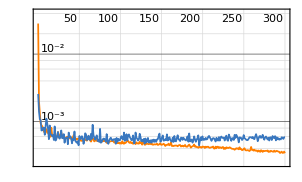
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:13500  rounds:300  time:2.9min  examples/s:311
data | ,,  training examples:180  validation examples:10  processed examples:54000  skipped examples:0
method | ,,  ADAMoptimizer  batch size4  GPUAll
round | ,,  loss:3.4×10^-4
validation | ,,  loss:5.84×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
netTrainResult=
NetTrain[
tn,
dataTrain,
All,
ValidationSet->dataValid,
BatchSize->4,
MaxTrainingRounds->300,
LossFunction->{"Loss"->Scaled[1]},
Method->{"ADAM",LearningRate->0.001},
TargetDevice->{"GPU",All},
WorkingPrecision->"Real32"
]
```

## Evaluation

```mathematica
quadRGBA[{{a_,b_},{c_,d_}}]:=Polygon[{a["p2d"],b["p2d"],d["p2d"],c["p2d"]},VertexColors->{a["rgba"],b["rgba"],d["rgba"],c["rgba"]}]
quadRGB[{{a_,b_},{c_,d_}}]:=Polygon[{a["p2d"],b["p2d"],d["p2d"],c["p2d"]},VertexColors->{a["rgb"],b["rgb"],d["rgb"],c["rgb"]}]
quadA[{{a_,b_},{c_,d_}}]:=Polygon[{a["p2d"],b["p2d"],d["p2d"],c["p2d"]},VertexColors->1-{a["a"],b["a"],d["a"],c["a"]}]
```

Retourne le plus d' information possible sur un pixel.
rgba : couleur rgb et alpha
rgb: couleur seulement
a: alpha seulement
p2d: point 2d dans le monde (x,y)

```mathematica
testFunction[net_,sample_]:=Block[{result,data},(
result=net[sample];
data=Join[result["rgba"],result["p2d"]];
data=Flatten[data,{{2},{3},{1}}];
Map[<|"rgba"->#[[1;;4]],"rgb"->#[[1;;3]],"a"->#[[4]],"p2d"->#[[5;;6]]|>&,data,{2}]
)]
```

### Unit Test

```mathematica
trained=netTrainResult["TrainedNet"]
```

NetGraph[…]

```mathematica
nb=25;
seeOut@dataTrain[[nb,"Target"]]
seeOut@trained[dataTrain[[nb]],TargetDevice->"GPU"]["Output"]
```

-Graphics-

-Graphics-

```mathematica
MeanError1D[targets_,outputs_]:=Module[{errorArray,meanError},
errorArray=Abs[targets-outputs];
meanError=errorArray// Flatten //Mean;
meanError];
```

```mathematica
c2i=LinearFractionalTransform[{{50,50,0},{0,1,0},{0,0,1}}];
i2c=InverseFunction[c2i];


errors={};


For[k=0,k<=1,k+=0.1,
c2wS=Table[place[{Cos[t],Sin[t]}*4,t+Pi/2],{t,k Degree,360 Degree,s Degree}]//N;
w2iS=InverseFunction[#.i2c]&/@c2wS;
is=Parallelize[snapshot[#,monde,100,0.25,{0,0,0}]&/@w2iS];
dataTest=MapThread[zap,{w2iS,is}];

Outputs=trained/@dataTest;
errorK=Mean[Table[MeanError1D[dataTest[[i,"Target"]],Outputs[[i,"Output"]]],{i,1,Length[dataTest],1}]];
AppendTo[errors,{k,errorK}];];

errorTable=Dataset[AssociationThread[{"k","Error"},#]&/@errors];
errorTable
```

{361}

{360}

{360}

{360}

«7 more identical outputs»

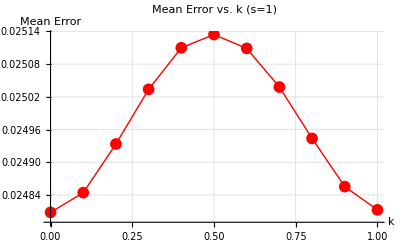

```mathematica
ListLinePlot[Normal[errorTable[All,{"k","Error"}]],PlotStyle->{Red,Thick},PlotMarkers->{"●",12},AxesLabel->{"k","Mean Error"},PlotLabel->"Mean Error vs. k (s=1)",GridLines->Automatic]
```

### Evaluate NERF

{100,71}

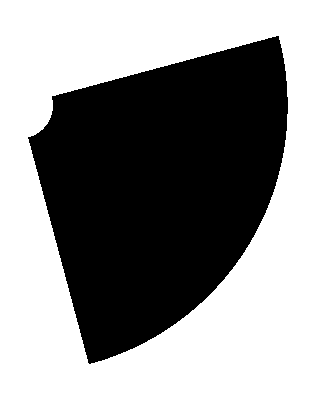

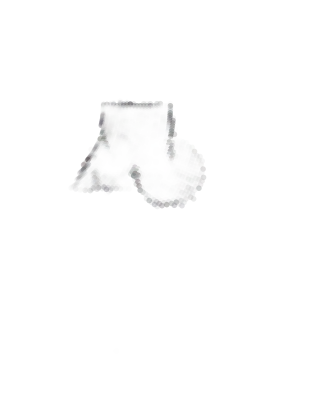

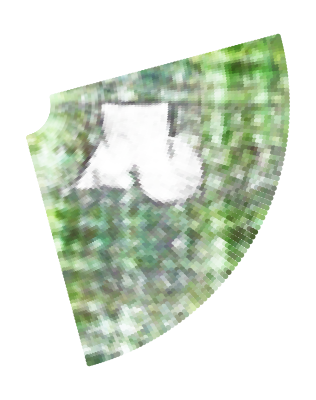

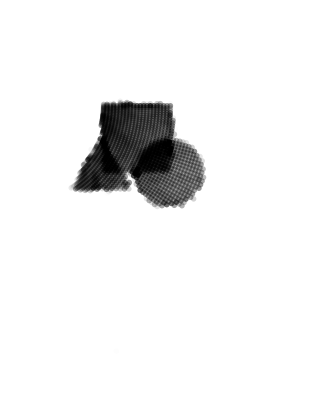

```mathematica
res=testFunction[trained,dataTest[[9]]];
res//Dimensions
Graphics[{PointSize[0.01],Map[quadRGBA,Partition[res,{2,2},{1,1}],{2}]}]
Graphics[{PointSize[0.01],Map[{RGBColor[#rgba],Point[#p2d]}&,res,{2}]}]
Graphics[{PointSize[0.01],Map[{RGBColor[#rgb],Point[#p2d]}&,res,{2}]}]
Graphics[{PointSize[0.01],Map[{GrayLevel[0,#a],Point[#p2d]}&,res,{2}]}]
```

```mathematica
Grid[Partition[seeOut/@dataTest[[All,"Target"]],UpTo[1]]]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

## Un peu d'exploration

### Reconstruction

Le monde exemple contient un carre rouge, un triangle vert, et un rond bleu.

Faites d’autres mondes pour tester un peu plus le nerf.
1. Un monde avec plus d’ objets avec une bonne variation dans les densités. (utilisez des densités <=1)
2. Un monde qui est beaucoup plus difficile a reconstruire (a votre gout)
     Dans ce cas, on veut que le reseau apprennent bien les images (donc la loss descend tres bas) mais ne donne pas une bonne reconstruction.

### Precision VS baseline

Faite une fonction qui calcule l’erreur moyenne du nerf sur un ensemble de test.
Faites un ensemble d’ entrainement avec un intervalle de s degres entre chaque camera (donc 0..360, step s)
Faites un ensemble de test avec un decallage k   (donc k...360 step s)

3. Faites un entrainement pour un step s=1, mais testez avec plusieurs (une dizaine) k,  entre k = 0 et k = s
     Affichez l' erreur moyenne obtenu pour differents k, et expliquez le resultats .

4. Refaites exactement la meme chose avec un S plus grand (par exemple 10). Expliquez le resultat.

### Ablation study

5. Changez l' architecture du reseau (les convolutions 128) pour autre chose et comparez les resultats.

6. Changez le “positional encoding” pour autre chose (une version plus simple, une plus complexe) et comparez les resultats.

7. Convertir un monde RGB en ton de gris (“ColorConvert[]”) et comparez le resultat de nerf sur les deux monde.

### Dernier detail

Vous avez remarqué que le “positional encoding” est seulement calcule sur x et y, mais pas sur la direction (voir l’article NERF).
8. A votre avis, quel est l’impact de cette omision? (Autrement dit, a quoi sert la direction? Dans quel cas est-ce que la direction est vraiment utile pour NERF?)